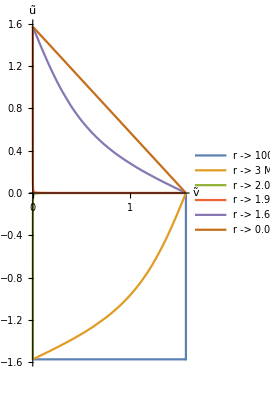
{-Graphics-,{{r -> 100 M, close to r→∞, ℐ^±,𝒾^*},{r -> 2.0001 M, close to r→2M, ũ|ṽ→0},{r -> 0.00001 M, close to r→0, singularity}}}

```mathematica
$plotPenroseKruskalSzekeres
```

```mathematica
$=$metricRindler={d[s]^2->-ρ^2 d[σ]^2+d[ρ]^2,ρ->1/a,σ->a τ[CG["observer's proper time"]],
{r->ρ Cosh[σ],t->ρ Sinh[σ]
}[CG["Minkowski relationship"]]}[CG["Rindler metric"]];
(ColumnForms[#1,2]&)[$]
$=$metricMinkowski/.d[Ω]->0//tuRule1
```

d[s]^2→d[ρ]^2-ρ^2 d[σ]^2
ρ→1/a
σ→a τ[observer's proper time]
{r→ρ Cosh[σ],t→ρ Sinh[σ]}[Minkowski relationship][Rindler metric]

d[s]^2→d[r]^2-d[t]^2

```mathematica
$s=$metricRindler//tuRule1//tuRuleSelect[t|r]
$/.$s//tudExpand[d]//Simplify
```

{r→ρ Cosh[σ],t→ρ Sinh[σ]}

d[s]^2→d[ρ]^2-ρ^2 d[σ]^2

```mathematica
$metricRindler
```

{d[s]^2→d[ρ]^2-ρ^2 d[σ]^2,ρ→1/a,σ→a τ[observer's proper time],{r→ρ Cosh[σ],t→ρ Sinh[σ]}[Minkowski relationship]}[Rindler metric]

```mathematica
GreenFunction[D[u[x, t], {t}] - D[u[x, t], {x, 2}], u[x, t], {x,-∞,∞}, t, {y, s}]
Plot3D[Evaluate[Table[%/.{y->1.5,s->i},{i,0.1001,0.5,0.1}]],{x,0,3},{t,0.1,0.5},PlotRange-> {0,4}]
```

(ⅇ^(-(x-y)^2/(4 (-s+t))) HeavisideTheta[-s+t])/(2 √π √(-s+t))

-Graphics3D-

(-m^2+□^2)·K[x,x']→-δ[x,x']

-UnderBar[∂]_r[UnderBar[∂]_r[u]]+UnderBar[∂]_t[UnderBar[∂]_t[u]]

UnderBar[∂]_(ⅈ σ+τ)[UnderBar[∂]_(ⅈ σ+τ)[u]]

UnderBar[∂]_(ⅈ σ)[UnderBar[∂]_(ⅈ σ)[u]]+UnderBar[∂]_τ[UnderBar[∂]_(ⅈ σ)[u]]+UnderBar[∂]_(ⅈ σ)[UnderBar[∂]_τ[u]]+UnderBar[∂]_τ[UnderBar[∂]_τ[u]]

```mathematica
$=$metricSchwarzschildDeSitter//tuRuleSelect[d[s]^2,f]//tuRule1
$=$/.xΩ->Subscript[Ω, 2]/.(tuCoordSolidAngle[2]//tuRule)
$g=$[[2]]//tuMetricProperTime
$geodesicEqn
```

d[s]^2→r^2 d[Ω]^2+d[r]^2/f[r]-d[t]^2 f[r]

d[s]^2→r^2 d[Ω]^2+d[r]^2/f[r]-d[t]^2 f[r]

{gvars→{Ω,r,t},g_ΩΩ^ΩΩ→r^2,g_Ωr^Ωr→0,g_Ωt^Ωt→0,g_rΩ^rΩ→0,g_rr^rr→1/f[r],g_rt^rt→0,g_tΩ^tΩ→0,g_tr^tr→0,g_tt^tt→-f[r],g_ΩΩ^ΩΩ→1/r^2,g_Ωr^Ωr→0,g_Ωt^Ωt→0,g_rΩ^rΩ→0,g_rr^rr→f[r],g_rt^rt→0,g_tΩ^tΩ→0,g_tr^tr→0,g_tt^tt→-1/f[r],detg→-r^2,gmatrixdd→{{r^2,0,0},{0,1/f[r],0},{0,0,-f[r]}},gmatrixuu→{{1/r^2,0,0},{0,f[r],0},{0,0,-1/f[r]}}}

{Γ_μρ$σ$^μρ$σ$ UnderBar[∂]_λ[x_ρ$^ρ$] UnderBar[∂]_λ[x_σ$^σ$]+UnderBar[∂]_λ[UnderBar[∂]_λ[x_μ^μ]]→0,Null}

```mathematica
$sf=$metricSchwarzschildDeSitter//tuRuleSelect[f[r],{a,b}]//tuRule1
```

f[r]→1-(2 a[M])/r-r^2 b[Λ]

```mathematica
$ds=$metricSchwarzschildDeSitter//tuRuleSelect[d[s]^2,{f}]//tuRule1
$=tuGeodesicEqn[$ds];(ColumnForms[#1,2]&)[$]
coord
metric;
$s=T[K,"u",{μ}]->{0,0,1}
$sl=$s//tuIndexLowerAll[μ,μ];
$sl[[2]]=$sl[[2]]//lower;
$={$sl,$s}//tuRuleOp[Dot]//(#/.toTimes&)
$sf=$metricSchwarzschildDeSitter//tuRuleSelect[f[r],{a,b}]//tuRule1
$=$/.$sf

$=$//.{a[aa_]->aa,b[bb_]->bb,Λ->0}
```

d[s]^2→r^2 d[Ω]^2+d[r]^2/f[r]-d[t]^2 f[r]

d[d[Ω]]→-(2 d[r] d[Ω])/r
d[d[r]]→r d[Ω]^2 f[r]+(d[r]^2 f'[r])/(2 f[r])-1/2 d[t]^2 f[r] f'[r]
d[d[t]]→-(d[r] d[t] f'[r])/f[r]

{Ω,r,t}

K_μ^μ→{0,0,1}

K_μ^μ K_μ^μ→-f[r]

f[r]→1-(2 a[M])/r-r^2 b[Λ]

K_μ^μ K_μ^μ→-1+(2 a[M])/r+r^2 b[Λ]

K_μ^μ K_μ^μ→-1+(2 M)/r

```mathematica
e[3,0]
```

e[3,0]

```mathematica
$->-κ{1,0,1}
```

{0,-1/r-f'[r]/(2 f[r]),0}→{-κ,0,-κ}

```mathematica
coord
metric//display
covariant[coord]//display
KK
hypersurface[t]
covariant[unitnormal]
\//
extrinsic
extrinsictrace
induced
HScoord
```

{r,t,Ω}

{Ω,Ω} | r^2
{r,r} | 1/(1-(2 G M)/r-(r^2 Λ)/3)
{t,t} | -1+(2 G M)/r+(r^2 Λ)/3

{r,r} | (3 G M-3 r+2 r^3 Λ)/(6 G M-3 r+r^3 Λ)
{Ω,Ω} | 1-2 G M r+r^2-(r^4 Λ)/3
{r,t}
{t,r} | (3 G M t-r^3 t Λ)/(6 G M r-3 r^2+r^4 Λ)
{t,t} | 1-((-3 G M+r^3 Λ) (6 G M-3 r+r^3 Λ))/(9 r^2)
{r,Ω}
{Ω,r} | -Ω/r

KK

{{0,0,0},{((3 G M-r^3 Λ) √(r/(18 G M-9 r+3 r^3 Λ)))/r^2,0,0},{0,0,0}}

```mathematica
$=$coordTortoise//tuRuleSelect[SuperStar[r],{u|v}]//tuRuleSolveF[{u,v}]
e[3,0]
```

{u→t-r^*,v→t+r^*}

{r_C→(-3 M Λ^2+√(Λ^3 (-1+9 M^2 Λ)))^(1/3) (1/Λ+1/((-3 M Λ^2+√(Λ^3 (-1+9 M^2 Λ)))^(2/3))),r_H→-(ⅈ (-(ⅈ+√3) Λ+(-ⅈ+√3) (-3 M Λ^2+√(Λ^3 (-1+9 M^2 Λ)))^(2/3)))/(2 Λ (-3 M Λ^2+√(Λ^3 (-1+9 M^2 Λ)))^(1/3))}

```mathematica
$=$g=e[1]
$=$/.d[s]->0/.d[Ω]->0
```

d[s]^2→d[r]^2/(1-(2 G M)/r-(r^2 Λ)/3)+(-1+(2 G M)/r+(r^2 Λ)/3) d[t]^2+r^2 d[Ω]^2

0→d[r]^2/(1-(2 G M)/r-(r^2 Λ)/3)+(-1+(2 G M)/r+(r^2 Λ)/3) d[t]^2

```mathematica
hypersurface[t]
unitnormal
covariant[unitnormal]
```

{0,1/(√3 √(r/(6 G M-3 r+r^3 Λ))),0}

{{0,0,0},{((3 G M-r^3 Λ) √(r/(18 G M-9 r+3 r^3 Λ)))/r^2,0,0},{0,0,0}}

```mathematica
coord
$=unitnormal
$1=lower[unitnormal]
covariant[unitnormal]
unitnormal.lower[covariant[unitnormal],{1}]//Simplify
coord.lower[covariant[{1,0,0}],{1}]//Simplify
```

{r,t,Ω}

{0,1/(√3 √(r/(6 G M-3 r+r^3 Λ))),0}

{0,(-1+(2 G M)/r+(r^2 Λ)/3)/(√3 √(r/(6 G M-3 r+r^3 Λ))),0}

{{0,0,0},{((3 G M-r^3 Λ) √(r/(18 G M-9 r+3 r^3 Λ)))/r^2,0,0},{0,0,0}}

{-((-3 G M+r^3 Λ) (6 G M-3 r+r^3 Λ))/(9 r^3),0,0}

{(r (9 G M-3 r^3 Λ))/((6 G M-3 r+r^3 Λ)^2),-(t (-3 G M+r^3 Λ) (6 G M-3 r+r^3 Λ)^2)/(27 r^4),r^2 (-2 G M+r-(r^3 Λ)/3) Ω}

```mathematica
$s=$=e[6.8]//tuRuleSelect[_ tuDCovariant[_,_]]//tuRule1
$=$/.μ->μ1;
$=T[χ,"u",{μ}]tuDCovariant[#,μ]&/@$//.tuDExpand[tuDOps,{κ}];
$=$/.$s;

$=$/.tt:T[χ,"u",{μ_}]->T[g,"uu",{μ,ν1}]·T[χ,"d",{ν1}]//.tuDExpand[tuDOps,{T[g,"uu",{μ_,ν1_}]}]//expandDC[];$//ColumnSumExp

$s1={tuDCovariant[T[χ,"d",{μ}],ν]+tuDCovariant[T[χ,"d",{ν}],μ]->0,(T[χ,"d",{μ}]tuDCovariant[T[χ,"d",{σ}],ν]//tuIndexAntiSymmetrize[{μ,σ}])->0}
```

χ_μ^μ UnderBar[∇]_μ[χ_ν^ν]→-κ χ_ν^ν

∑[g_μ1ν1^μ1ν1·UnderBar[∇]_μ[χ_ν1^ν1] g_νν1^νν1·UnderBar[∇]_μ1[χ_ν1^ν1]
g_μ1ν1^μ1ν1·χ_ν1^ν1 g_νν1^νν1·UnderBar[∇]_μ[UnderBar[∇]_μ1[χ_ν1^ν1]]] g_μν1^μν1·χ_ν1^ν1→κ^2 g_νν1^νν1·χ_ν1^ν1

{UnderBar[∇]_ν[χ_μ^μ]+UnderBar[∇]_μ[χ_ν^ν]→0,1/2 (-χ_σ^σ UnderBar[∇]_ν[χ_μ^μ]+χ_μ^μ UnderBar[∇]_ν[χ_σ^σ])→0}

```mathematica
coord={t,r,Ω}
$coord=<|Thread[coord->{1,2,3}]|>

$ds=d[s]^2->Sum[T[g,"uu",{$coord[i],$coord[j]}][Apply[Sequence,coord]]d[i]d[j],{i,coord},{j,coord}]
tuGeodesicEqn[$ds]//Length
Christoffel
//
coord={t,r,Ω}
metric=Table[T[g,"uu",{i,j}][t,r,Ω],{i,coord},{j,coord}]
<<diffgeo`diffgeo`
```

{t,r,Ω}

<|t→1,r→2,Ω→3|>

d[s]^2→d[t]^2 g_11^11[t,r,Ω]+d[r] d[t] g_12^12[t,r,Ω]+d[t] d[Ω] g_13^13[t,r,Ω]+d[r] d[t] g_21^21[t,r,Ω]+d[r]^2 g_22^22[t,r,Ω]+d[r] d[Ω] g_23^23[t,r,Ω]+d[t] d[Ω] g_31^31[t,r,Ω]+d[r] d[Ω] g_32^32[t,r,Ω]+d[Ω]^2 g_33^33[t,r,Ω]

3

```mathematica
$geodesicEqn;
PR["Example of Computing surface gravity with diffgeo using metric: ",$ds=$metricSchwarzschildDeSitter//tuRuleSelect[d[s]^2,{f}]//tuRule1,
$=tuGeodesicEqn[$ds];
NL,"The coordinates: ",coord,
NL,"By inspection of the metric the Killing bases are ",{tuDPartial[_,Ω],tuDPartial[_,t]},
NL,"Let the Killing vector ",$s=T[K,"u",{μ}]->{0,0,1},
NL,"Compute the LHS of e[6.8] for each ν: ",$e=e[6.8]//tuRuleSelect[_ tuDCovariant[_,μ],{κ},{κ^2}]//First,

Yield,$=raise[{1,1,1}].covariant[{0,0,1}]//Simplify,
NL,"Focus on the t-Killing vector ",$=$//Last,
NL,"Use $metricSchwarzschildDeSitter for f[r]: ",$sf=$metricSchwarzschildDeSitter//tuRuleSelect[f[r],{a,b}]//tuRule1;
$sf={$sf,(D[#,r]&/@$sf)},
Yield,$=$/.$sf//Simplify,
NL,"If ",$s={a[aa_]->aa,b[bb_]->bb},
Yield,$=($e/.ν->t)->($1=$//.$s),
Imply,$=κ->-$1;$//Framed

]
```

Example of Computing surface gravity with diffgeo using metric: d[s]^2→r^2 d[Ω]^2+d[r]^2/f[r]-d[t]^2 f[r]
The coordinates: {Ω,r,t}
By inspection of the metric the Killing bases are {UnderBar[∂]_Ω[_],UnderBar[∂]_t[_]}
Let the Killing vector K_μ^μ→{0,0,1}
Compute the LHS of e[6.8] for each ν: χ_μ^μ UnderBar[∇]_μ[χ_ν^ν]→-κ χ_ν^ν
→ {0,f'[r]/(2 f[r]^2),-1/2 f'[r]}
Focus on the t-Killing vector -1/2 f'[r]
Use $metricSchwarzschildDeSitter for f[r]: {f[r]→1-(2 a[M])/r-r^2 b[Λ],f'[r]→(2 a[M])/r^2-2 r b[Λ]}
→ -a[M]/r^2+r b[Λ]
If {a[aa_]→aa,b[bb_]→bb}
→ (χ_μ^μ UnderBar[∇]_μ[χ_t^t]→-κ χ_t^t)→-M/r^2+r Λ
⇒ κ→M/r^2-r Λ

```mathematica
$κ
e[3,0]
```

κ→M/r^2-r Λ

{r_C→(-3 M Λ^2+√(Λ^3 (-1+9 M^2 Λ)))^(1/3) (1/Λ+1/((-3 M Λ^2+√(Λ^3 (-1+9 M^2 Λ)))^(2/3))),r_H→-(ⅈ (-(ⅈ+√3) Λ+(-ⅈ+√3) (-3 M Λ^2+√(Λ^3 (-1+9 M^2 Λ)))^(2/3)))/(2 Λ (-3 M Λ^2+√(Λ^3 (-1+9 M^2 Λ)))^(1/3))}

```mathematica
?outer
```

outer[ tensor1, tensor2, ... ] or tensor1 ** tensor2 ** ...  gives the outer product of an arbitrary number of tensors.

```mathematica
$k={0,0,1}
$kl=lower[$k]
$=$k.$kl
$=$//.$sf
$/.{a[aa_]->aa,b[bb_]->bb,Λ->0,r->2 M}
$sf
```

{0,0,1}

{0,0,-f[r]}

-f[r]

-1+(2 a[M])/r+r^2 b[Λ]

4 M^2 Λ

{f[r]→1-(2 a[M])/r-r^2 b[Λ],f'[r]→(2 a[M])/r^2-2 r b[Λ]}

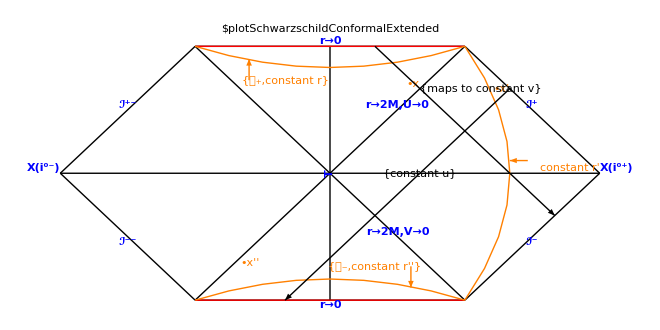

```mathematica
tuGraphicDefs;
define$pt[3,3];
$offset=.3;

Graphics[MapIndexed[Text[#2,#1]&,$pt]];

$line={{mid[34,40],$pt[[46]]},
{mid[30,38],$pt[[46]]},

{$pt[[25]],mid[26,27]},
{mid[23,24],$pt[[25]]},

{mid[10,16],$pt[[25]]},
{mid[12,20],mid[34,40]},(**)

{mid[10,16],mid[30,38]},
{$pt[[25]],mid[30,38]},

{mid[12,20],$pt[[25]]},
{$pt[[25]],mid[34,40]},

{$pt[[4]],$pt[[25]]},
{$pt[[25]],$pt[[46]]},
{$pt[[4]],mid[12,20]},
{$pt[[4]],mid[10,16]}

};

Graphics[{Thin,Black,Map[Line[#]&,$line],
Thick,Red,Line[$line[[6]]],Line[$line[[7]]],
Blue,
(*
MapIndexed[Text[#2,(#1[[1]]+#1[[2]])/2]&,$line],*)(*line numbering*)

Text[Style[T,Bold,Medium],$pt[[25]],{0,-$offset},{0,1}],
Text[Style[X[ii^("0+")],Bold,Medium],$pt[[46]],{-4 $offset,-2 $offset}],
Text[Style[X[ii^("0-")],Bold,Medium],$pt[[4]],{4 $offset,-2 $offset}],

Text[Style["ℐ^-",Bold,Medium],midline[2],{ $offset,2 $offset},{1,1}],
Text[Style["ℐ^(--)",Bold,Medium],midline[14],{ $offset,2 $offset},{1,-1}],

Text[Style["ℐ^+",Bold,Medium],midline[1],{$offset,-3 $offset},{1,-1}],
Text[Style["ℐ^(+-)",Bold,Medium],midline[13],{$offset,-3 $offset},{1,1}],
Text[Style["r→0",Bold,Medium],midline[6],{$offset,-3 $offset},{1,0}],
Text[Style["r→0",Bold,Medium],midline[7],{$offset,3 $offset},{1,0}],
Text[Style["r→2M,U→0",Bold,Medium],midline[10],{$offset,-3 $offset},{1,1}],
Text[Style["r→2M,V→0",Bold,Medium],midline[8],{$offset,-3 $offset},{1,-1}],
(**)
Thin,Orange,
BezierCurve[{mid[34,40],mid[39,46],mid[30,38]}],
Text[Style["•x'",Medium],mid[39,40,0],{4$offset,0},{1,0}],
Text[Style["constant r'",Small],$pt[[46]],{5$offset,-10 $offset},{1,0}],
Thin,Arrowheads[.015],Arrow[{{2.2,.15},{2,.15}}],

BezierCurve[{mid[12,20],{0,1},mid[34,40]}],
Text[Style["•x",Medium],$pt[[33]],{10$offset,-14$offset},{1,0}],
Text[Style[{SubPlus[𝒞],"constant r"},Small],{-.5,1.1},{0$offset,-0 $offset},{1,0}],
Arrowheads[.015],Arrow[{{-.9,1.1},{-.9,1.35}}],

BezierCurve[{mid[9,17],{0,-1},mid[30,38]}],
Text[Style["•x''",Medium],$pt[[17]],{-10$offset,14$offset},{1,0}],
Text[Style[{SubMinus[𝒞],"constant r''"},Small],{.5,-1.1},{0$offset,-0 $offset},{1,0}],
Arrowheads[.015],Arrow[{{.9,-1.1},{.9,-1.35}}],
(*
Arrowheads[{-.015,.015}],Dashed,Arrow[{{.71,1.25},{-0.65,-1.25}}],
Text[Style[{t->t-4π M G I,"corresponence"},Small],{.07,-.1},{0$offset,-0 $offset},{1,1.9}],*)
(**)
Arrowheads[{.02,.02}],Black,Arrow[{$pt[[40]],mid[16,24]}],
Text[Style[{"constant u"},Small],$pt[[32]],{0$offset,-1 $offset},{1,1}],
(**)
Arrowheads[{.02,.02}],Black,Arrow[{mid[26,34],mid[39,45]}],
Text[Style[{"maps to constant v"},Small],$pt[[33]],{-6$offset, -1$offset},{1,-1}],

Blue,Text[
"The amplitude for a black hole to emit particles which are detected in a mode of energy E 
by an observer in region I may be related to the integral e[4.4] of Exp[-𝕚Et] times the propagator 
to go from a point x on a complex surface 𝒞_+ of constant r in region II 
to a point x' on the detector's world line in region I. 
The integral e[4.4] is over t on 𝒞_+. 
The propagator is analytic in t except when Im[t]→0 and x is connected to ℂ_+ by a null [Complex??] geodesic
[Is this the s[x,x']→0 case?].
It is shown that if Im[x]→4πM ⇒ x ⟷ {x'' in region III}. 
There is a similar correspondence between the singularities of the propagator.",

{-.5,-2},{0,1}]
},PlotLabel->"$plotSchwarzschildConformalExtended"
]
```

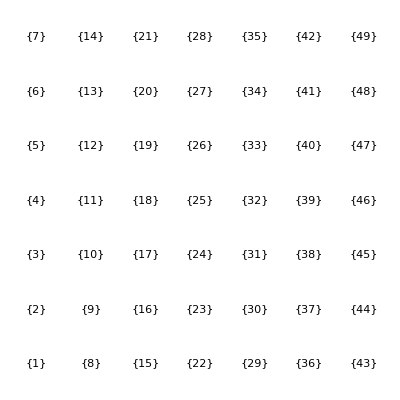

{{{-3,-3},{-3,-2},{-3,-1},{-3,0},{-3,1},{-3,2},{-3,3},{-2,-3},{-2,-2},{-2,-1},{-2,0},{-2,1},{-2,2},{-2,3},{-1,-3},{-1,-2},{-1,-1},{-1,0},{-1,1},{-1,2},{-1,3},{0,-3},{0,-2},{0,-1},{0,0},{0,1},{0,2},{0,3},{1,-3},{1,-2},{1,-1},{1,0},{1,1},{1,2},{1,3},{2,-3},{2,-2},{2,-1},{2,0},{2,1},{2,2},{2,3},{3,-3},{3,-2},{3,-1},{3,0},{3,1},{3,2},{3,3}}[40],{{-3,-3},{-3,-2},{-3,-1},{-3,0},{-3,1},{-3,2},{-3,3},{-2,-3},{-2,-2},{-2,-1},{-2,0},{-2,1},{-2,2},{-2,3},{-1,-3},{-1,-2},{-1,-1},{-1,0},{-1,1},{-1,2},{-1,3},{0,-3},{0,-2},{0,-1},{0,0},{0,1},{0,2},{0,3},{1,-3},{1,-2},{1,-1},{1,0},{1,1},{1,2},{1,3},{2,-3},{2,-2},{2,-1},{2,0},{2,1},{2,2},{2,3},{3,-3},{3,-2},{3,-1},{3,0},{3,1},{3,2},{3,3}}[16]}

```mathematica
Graphics[MapIndexed[Text[#2,#1]&,$pt]]
{$pt[40],$pt[16]}
```

```mathematica
$=$metricSchwarzschildKruskalSzekeres;(ColumnForms[#1,2]&)[$]
```

{{T→ⅇ^(r/(4 G M)) √Abs[-1+r/(2 G M)] (Cosh[t/(4 G M)] HeavisideTheta[2 G M-r]+HeavisideTheta[-2 G M+r] Sinh[t/(4 G M)]),X→ⅇ^(r/(4 G M)) √Abs[-1+r/(2 G M)] (Cosh[t/(4 G M)] HeavisideTheta[-2 G M+r]+HeavisideTheta[2 G M-r] Sinh[t/(4 G M)])}}[$coordSchwarzschildKruskalSzekeres]
{T^2-X^2→ⅇ^(r/(2 G M)) Abs[1-r/(2 G M)] (HeavisideTheta[2 G M-r]^2-HeavisideTheta[-2 G M+r]^2)}[Null geodesic at r→2MG]
Refine[T^2-X^2→ⅇ^(r/(2 G M)) Abs[1-r/(2 G M)] (HeavisideTheta[2 G M-r]^2-HeavisideTheta[-2 G M+r]^2),r>2 G M]
r→2 (G M+G M ProductLog[(T^2-X^2)/ⅇ])
T→ⅇ^(r/(4 G M)) √Abs[-1+r/(2 G M)] Sinh[t/(4 G M)]
X→ⅇ^(r/(4 G M)) √Abs[-1+r/(2 G M)] Cosh[t/(4 G M)]
r→2 (G M+G M ProductLog[(T^2-X^2)/ⅇ])
t→4 G M ArcSinh[(ⅇ^(1/2 (-1-ProductLog[((T-X) (T+X))/ⅇ])) T)/(√Abs[ProductLog[((T-X) (T+X))/ⅇ]])]
{-d[T]^2+d[X]^2→(ⅇ^(r/(2 G M)) (-r^2 d[r]^2+(-2 G M+r)^2 d[t]^2))/(32 G^3 M^3 (2 G M-r)),-(32 ⅇ^(-r/(2 G M)) G^3 M^3 (d[T]^2-d[X]^2))/r→-(r d[r]^2)/(2 G M-r)+(-1+(2 G M)/r) d[t]^2}[$metricKrukalSzekeres]
{{T→(U+V)/2,X→1/2 (-U+V)},{-d[U] d[V]→(ⅇ^(r/(2 G M)) (-r^2 d[r]^2+(-2 G M+r)^2 d[t]^2))/(32 G^3 M^3 (2 G M-r)),-(32 ⅇ^(-r/(2 G M)) G^3 M^3 d[U] d[V])/r→-(r d[r]^2)/(2 G M-r)+((2 G M-r) d[t]^2)/r},{U→ⅇ^((r-t)/(4 G M)) √Abs[1-r/(2 G M)] (HeavisideTheta[2 G M-r]-HeavisideTheta[-2 G M+r]),V→ⅇ^((r+t)/(4 G M)) √Abs[1-r/(2 G M)] (HeavisideTheta[2 G M-r]+HeavisideTheta[-2 G M+r])}}[$metricKrukalSzekeresNull]

```mathematica
$coordSchwarzschildKruskalSzekeres
$metricEddingtonFinkelstein
```

{{T→ⅇ^(r/(4 G M)) √Abs[-1+r/(2 G M)] (Cosh[t/(4 G M)] HeavisideTheta[2 G M-r]+HeavisideTheta[-2 G M+r] Sinh[t/(4 G M)]),X→ⅇ^(r/(4 G M)) √Abs[-1+r/(2 G M)] (Cosh[t/(4 G M)] HeavisideTheta[-2 G M+r]+HeavisideTheta[2 G M-r] Sinh[t/(4 G M)])}}[$coordSchwarzschildKruskalSzekeres]

```mathematica
$=$metricPenrose//tuRuleSelect[{ũ,ṽ}]//Reverse
$=(d/@#&/@$)//tudExpandvI[d]
$s=$metricSchwarzschildKruskalSzekeres//tuRuleSelect[{U,V}]//(#/.U->u/.V->v&)
$s=$s/.r->ρ 2 G M/.t->τ 2 G M//Simplify
$=$//tuRuleApply[$s];
$=$/.{HeavisideTheta[a_]+HeavisideTheta[b_]:>1/;a===-b,HeavisideTheta[a_]-HeavisideTheta[b_]:>-1/;a===-b}//Refine[#,ρ>1]&;
$=$//tuRuleDivide//Simplify
$=$//tudExpandvI[d]//Simplify
```

{ṽ→ArcTan[v],ũ→ArcTan[u]}

{d[ṽ]→d[v]/(1+v^2),d[ũ]→d[u]/(1+u^2)}

{u→ⅇ^((r-t)/(4 G M)) √Abs[1-r/(2 G M)] (HeavisideTheta[2 G M-r]-HeavisideTheta[-2 G M+r]),v→ⅇ^((r+t)/(4 G M)) √Abs[1-r/(2 G M)] (HeavisideTheta[2 G M-r]+HeavisideTheta[-2 G M+r])}

{u→ⅇ^((ρ-τ)/2) √Abs[1-ρ] (HeavisideTheta[-2 G M (-1+ρ)]-HeavisideTheta[2 G M (-1+ρ)]),v→ⅇ^((ρ+τ)/2) √Abs[1-ρ] (HeavisideTheta[-2 G M (-1+ρ)]+HeavisideTheta[2 G M (-1+ρ)])}

d[ṽ]/d[ũ]→((1+ⅇ^(ρ-τ) (-1+ρ)) d[ⅇ^((ρ+τ)/2) √(-1+ρ)])/((1+ⅇ^(ρ+τ) (-1+ρ)) d[-ⅇ^((ρ-τ)/2) √(-1+ρ)])

(IIII$87202^(0,1)[2])/(IIII$87202^(0,1)[1])→-((ⅇ^τ+ⅇ^ρ (-1+ρ)) (ρ d[ρ]+(-1+ρ) d[τ]))/((1+ⅇ^(ρ+τ) (-1+ρ)) (ρ d[ρ]+d[τ]-ρ d[τ]))

ũ→ArcTan[ⅇ^(r/2) √Abs[-1+r] HeavisideTheta[1-r]-ⅇ^(r/2) √Abs[-1+r] HeavisideTheta[-1+r]]
ṽ→ArcTan[ⅇ^(r/2) √Abs[-1+r] HeavisideTheta[1-r]+ⅇ^(r/2) √Abs[-1+r] HeavisideTheta[-1+r]]

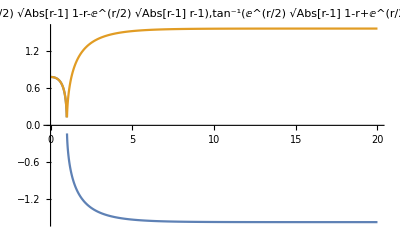

```mathematica
$=$metricPenroseSchwarzschildKruskalSzekeres//tuRuleSelect[{ũ,ṽ},{r}]//tuRule1;(ColumnForms[#1,2]&)[$];
$=$/.G->1/(2M)/.t->0//Expand;(ColumnForms[#1,2]&)[$]
$=#[[2]]&/@$;
Plot[$,{r,0,20},PlotLabel->$]
```

```mathematica
PR["What is{r,t}[constant ũ]",$=$pass[[1]];
]
$=$/.r->2M G σ/.t->2M G τ//Simplify
"outside BH"
$=$//Refine[#,σ>1&&G>0&&M>0]&//FullSimplify
$=$//tuRuleSolveF[τ]//Refine[#,C[1]==0&&ũ∈Reals&&-π/2<ũ<π/2]&//tuRule1

$[[1]]->Series[$[[2]],{ũ,0,1}]
```

What is{r,t}[constant ũ]Null

ũ→-ArcTan[ⅇ^(σ/2) √Abs[-1+σ] (-HeavisideTheta[-2 G M (-1+σ)]+HeavisideTheta[2 G M (-1+σ)]) (Cosh[τ/2]-Sinh[τ/2])]

outside BH

ũ→-ArcTan[ⅇ^((σ-τ)/2) √(-1+σ)]

τ→σ-2 Log[-Tan[ũ]/(√(-1+σ))]

τ→(σ-2 Log[-(ũ)/(√(-1+σ))])+O[ũ]^2

```mathematica
$0=$pass/.r->ρ 2 G M/.t->τ 2 G M/.- 2G M->-1/. 2G M->1//Simplify;
$u=$0[[1]];
$v=$0[[2]];
d/@$v//tudExpandvI[d]//Simplify

tuRuleIndependentVarPattern
```

d[ṽ]→(ⅇ^(ρ/2) (HeavisideTheta[1-ρ]+HeavisideTheta[-1+ρ]) (Abs[-1+ρ] (d[ρ]+d[τ])+d[ρ] Abs'[-1+ρ]))/(2 √Abs[-1+ρ] (Cosh[τ/2]-Sinh[τ/2]+ⅇ^ρ Abs[-1+ρ] (HeavisideTheta[1-ρ]+HeavisideTheta[-1+ρ])^2 (Cosh[τ/2]+Sinh[τ/2])))

{__+,__-,_^+,_^-,___,_^_,OverBar[_],UnderBar[_],OverTilde[_],OverHat[_],__*,_^*,OverVector[_],OverDot[_],OverDot[_],OverDoubleDot[_],_',_'',Tensor[_,_,_],Sign[_],__}

Extended conformal spacetime{T[-π,π],X[-π,π]} diagram centered on T-dependent formation of a BH Fig.12.2.  The diagram show the fate of null rays(±45°lines) from ℐ^-.
• One can interpret this diagram as if constant flux of radial waves from ℐ^- passing through r→0 and proceding to ℐ^+ if there is no BH.  If there is a BH then the radial flux disappears into the horizon at r→2MG.

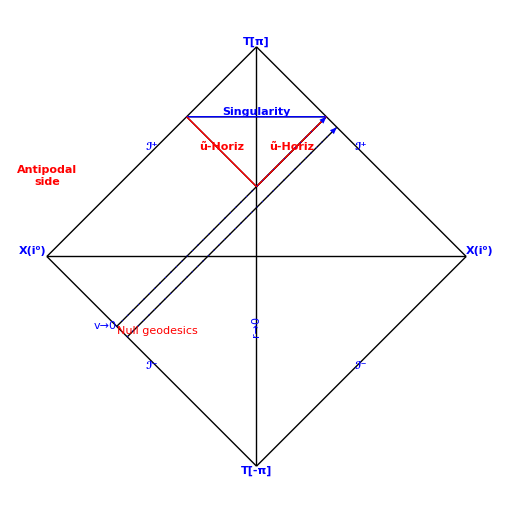

```mathematica
PR["Extended conformal spacetime{T[-π,π],X[-π,π]} diagram centered on T-dependent formation of a BH Fig.12.2.  The diagram show the fate of null rays(±45°lines) from ℐ^-.
• One can interpret this diagram as if constant flux of radial waves from ℐ^- passing through r→0 and proceding to ℐ^+ if there is no BH.  If there is a BH then the radial flux disappears into the horizon at r→2MG."];

$pt={Range[-3,3],Range[-3,3]}//Tuples;
$offset=.3;
Graphics[MapIndexed[Text[#2,#1]&,$pt]];

$line={{$pt[[28]],$pt[[46]]},
{$pt[[22]],$pt[[46]]},
{$pt[[22]],$pt[[28]]},
{$pt[[26]],$pt[[34]]},
{$pt[[20]],$pt[[34]]},
{$pt[[4]],$pt[[46]]},
{$pt[[4]],$pt[[28]]},
{$pt[[4]],$pt[[22]]},
{$pt[[26]],$pt[[20]]},
{$pt[[10]],$pt[[34]]},
{$pt[[10]]+.5{$offset,-$offset},$pt[[34]]+.5{$offset,-$offset}}

};
Graphics[{Thin,Black,Map[Line[#]&,$line],
Thick,Blue,Line[$line[[5]]],
Red,Line[$line[[4]]],Line[$line[[9]]],
Blue,
(*
MapIndexed[Text[Style[#2,Orange,Small],(#1[[1]]+#1[[2]])/2]&,$line],*)

Text[Style["T[π]",Bold,Medium],$pt[[28]],{-0 $offset,-2 $offset},{1,0}],Text[Style["T[-π]",Bold,Medium],$pt[[22]],{-0 $offset,2 $offset},{1,0}],
Text[Style[r->0,Medium],$pt[[24]],{0$offset,0 $offset},{0,1}],
Text[Style[X["i^0"],Bold,Medium],$pt[[46]],{-4 $offset,-2 $offset}],
Text[Style[X["i^0"],Bold,Medium],$pt[[4]],{3 $offset,-2 $offset}],
Text[Style["ℐ^-",Bold,Medium],midline[2],{ $offset,3 $offset},{1,1}],
Text[Style["ℐ^-",Bold,Medium],midline[8],{ $offset,3 $offset},{1,-1}],
Text[Style["ℐ^+",Bold,Medium],midline[1],{$offset,-3 $offset},{1,-1}],
Text[Style["ℐ^+",Bold,Medium],midline[7],{$offset,-3 $offset},{1,1}],
Text[Style["Singularity",Bold,Medium],midline[5],{0 $offset,-2$offset},{1,0}],
Text[Style["ũ-Horiz",Bold,Medium,Red],midline[4],{0 $offset,-4$offset},{1,1}],
Text[Style["ũ-Horiz",Bold,Medium,Red],midline[9],{0 $offset,-4$offset},{1,-1}],
Text[Style["Antipodal\nside",Bold,Medium,Red],$pt[[5]],{0 $offset,-2$offset},{1,-0}],

Thick,Dotted,Arrowheads[0.02],Arrow[$line[[11]]],Arrow[$line[[10]]],
Text[Style["Null geodesics",Medium,Red],$pt[[10]],{-1,1},{1,1}],
Text[Style[v->0,Medium,Blue],$pt[[10]],{1,0},{1,1}]
}
]
```

```mathematica
$v=V->($eom//tuRule1//Part[#,1,1]&//Coefficient[#,f]&)
$limit={{r->2G M},{r->∞}}
$=Table[V[Apply[Sequence,$limit[[i]]]]->Limit[$v[[2]],$limit[[i]]],{i,1,2}];{$v,(ColumnForms[#1,2]&)[$],}
```

V→(1-(2 G M)/r) (m^2+(2 G M)/r^3+(l (1+l))/r^2)

{{r→2 G M},{r→∞}}

{V→(1-(2 G M)/r) (m^2+(2 G M)/r^3+(l (1+l))/r^2),V[r→2 G M]→0
V[r→∞]→m^2,Null}

```mathematica
tuRuleSelect[{r,SuperStar[r]},{},{}][e[14.3,1]]
e[14.3,1]
```

{r→2 (G M+G M ProductLog[ⅇ^(-1+r^*/(2 G M))]),r→2 G M,r^*→-∞}

{f (1-(2 G M)/r) (m^2+(2 G M)/r^3+(l (1+l))/r^2)+UnderBar[∂]_t[UnderBar[∂]_t[f]]-UnderBar[∂]_(r^*)[UnderBar[∂]_(r^*)[f]]→0,ϕ→(f[r,t] SphericalHarmonicY[l,m,θ,φ])/r,r→2 (G M+G M ProductLog[ⅇ^(-1+r^*/(2 G M))]),{r^*→-∞,r→2 G M,{UnderBar[∂]_t[UnderBar[∂]_t[f]]-UnderBar[∂]_(r^*)[UnderBar[∂]_(r^*)[f]]→0}[free wave,solutions Exp[-Iωu], Exp[-Iωv]]}}[e[14.3,1] radial component of e[14.2,4]]

```mathematica
$metricKrukalSzekeresNull
$metricSchwarzschildKruskalSzekeres;
$metricEddingtonFinkelstein
$metricNullCoordinateMinkowski;
```

{{T→(U-V)/2,X→(U+V)/2},{d[U] d[V]→(ⅇ^(r/(2 G M)) (-r^2 d[r]^2+(-2 G M+r)^2 d[t]^2))/(32 G^3 M^3 (2 G M-r)),(32 ⅇ^(-r/(2 G M)) G^3 M^3 d[U] d[V])/r→-(r d[r]^2)/(2 G M-r)+((2 G M-r) d[t]^2)/r}}

{{{v→t+r^*[tortoise coordinate]}[ingoing null ray],{u→t-r^*[tortoise coordinate]}[outgoing null ray]},{r^*[tortoise coordinate]→r+2 G M Log[Abs[-1+r/(2 G M)]],r→2 (G M+G M ProductLog[ⅇ^(-1+r^*/(2 G M))]),ProductLog[ⅇ^(-1+r^*/(2 G M))]→-1+r/(2 G M),r^*→2 (G M+G M Log[(ⅇ^(-1+r/(2 G M)) (-2 G M+r))/(2 G M)]),{r^*→-t+v,r→2 (G M+G M ProductLog[ⅇ^(-1+(-t+v)/(2 G M))]),{d[s]^2→2 d[r] d[v]+(-1+(2 G M)/r) d[v]^2+r^2 (d[θ]^2+d[ϕ]^2 Sin[θ]^2)}[$metricEddingtonFinkelsteinIn]},{r^*→t-u,r→2 (G M+G M ProductLog[ⅇ^(-1+(t-u)/(2 G M))]),{d[s]^2→-2 d[r] d[u]+(-1+(2 G M)/r) d[u]^2+r^2 (d[θ]^2+d[ϕ]^2 Sin[θ]^2)}[$metricEddingtonFinkelsteinOut]}}}

```mathematica
$s=$=$metricSchwarzschildKruskalSzekeres//tuRuleSelect[{T,X}];
$=$//tuRuleSolveF[{U,V}];
$=$/.$s//FullSimplify//Refine[#,r>2G M]&;
$s=$metricNullCoordinateMinkowski//tuRuleSelect[u]//tuRuleSolveF[{r,t}];
$=$/.$s
```

{U→ⅇ^((2 r+u)/(4 G M)) √Abs[1-r/(2 G M)],V→ⅇ^(-u/(4 G M)) √Abs[1-r/(2 G M)]}

```mathematica
$=$tmp/.($metricEddingtonFinkelstein//tuRuleSelect[{r},{SuperStar[r]}])//FullSimplify//ExpandAll
$=$/. Exp[a_]->xExp[a]//.xExp[a_+b_]->xExp[a]xExp[b]
$=$/.xExp[a_]:>FullSimplify[Exp[a]]
```

{U→ⅇ^((r+t)/(4 G M)) √Abs[1-r/(2 G M)],V→ⅇ^((r-t)/(4 G M)) √Abs[1-r/(2 G M)]}

{t→r+u}

{u→4 G M Log[(√Abs[1-r/(2 G M)])/V]}

a V^(4 ⅈ G M ω) Abs[1-r/(2 G M)]^(-2 ⅈ G M ω)

f[ω]→a (V/(√Abs[1-r/(2 G M)]))^(4 ⅈ G M ω)

{U→ⅇ^(1/2+t/(4 G M)+1/2 ProductLog[ⅇ^(-1+r^*/(2 G M))]) √Abs[ProductLog[ⅇ^(-1+r^*/(2 G M))]],V→ⅇ^(1/2-t/(4 G M)+1/2 ProductLog[ⅇ^(-1+r^*/(2 G M))]) √Abs[ProductLog[ⅇ^(-1+r^*/(2 G M))]]}

{U→√Abs[ProductLog[xExp[-1] xExp[r^*/(2 G M)]]] xExp[1/2] xExp[t/(4 G M)] xExp[1/2 ProductLog[ⅇ^(-1+r^*/(2 G M))]],V→√Abs[ProductLog[xExp[-1] xExp[r^*/(2 G M)]]] xExp[1/2] xExp[-t/(4 G M)] xExp[1/2 ProductLog[ⅇ^(-1+r^*/(2 G M))]]}

{U→ⅇ^(1/2+t/(4 G M)+1/2 ProductLog[ⅇ^(-1+r^*/(2 G M))]) √Abs[ProductLog[ⅇ^(-1+r^*/(2 G M))]],V→ⅇ^(1/2-t/(4 G M)+1/2 ProductLog[ⅇ^(-1+r^*/(2 G M))]) √Abs[ProductLog[ⅇ^(-1+r^*/(2 G M))]]}

```mathematica
$sV
```

V/Sqrt[_]→α λ

```mathematica
Get[$InitialDirectory<>"/Mathematica/Gravity/gravityDefinitions.out"]
```

{Temporary}

```mathematica
$metricPenroseSchwarzschildKruskalSzekeres
```

{{{v→Tan[ṽ],u→Tan[ũ],{ṽ,ũ}∈Interval[{-π/2,π/2}]}[$coordPenrose],{ṽ→ArcTan[v],ũ→ArcTan[u]},d[s]^2→1/4 d[Ω]^2 (Tan[ũ]-Tan[ṽ])^2},{u→T-X,v→T+X},{T→ⅇ^(r/(4 G M)) √Abs[-1+r/(2 G M)] (Cosh[t/(4 G M)] HeavisideTheta[2 G M-r]+HeavisideTheta[-2 G M+r] Sinh[t/(4 G M)]),X→ⅇ^(r/(4 G M)) √Abs[-1+r/(2 G M)] (Cosh[t/(4 G M)] HeavisideTheta[-2 G M+r]+HeavisideTheta[2 G M-r] Sinh[t/(4 G M)])},{ṽ→ArcTan[ⅇ^(r/(4 G M)) √Abs[-1+r/(2 G M)] (Cosh[t/(4 G M)] HeavisideTheta[-2 G M+r]+HeavisideTheta[2 G M-r] Sinh[t/(4 G M)])+ⅇ^(r/(4 G M)) √Abs[-1+r/(2 G M)] (Cosh[t/(4 G M)] HeavisideTheta[2 G M-r]+HeavisideTheta[-2 G M+r] Sinh[t/(4 G M)])],ũ→-ArcTan[ⅇ^(r/(4 G M)) √Abs[-1+r/(2 G M)] (Cosh[t/(4 G M)] HeavisideTheta[-2 G M+r]+HeavisideTheta[2 G M-r] Sinh[t/(4 G M)])-ⅇ^(r/(4 G M)) √Abs[-1+r/(2 G M)] (Cosh[t/(4 G M)] HeavisideTheta[2 G M-r]+HeavisideTheta[-2 G M+r] Sinh[t/(4 G M)])]}}

```mathematica
PR["Penrose diagram for $metricSchwarzschildKruskalSzekeres",
NL,"$coordSchwarzschildKruskalSzekeres ",$0=tuRule[$coordSchwarzschildKruskalSzekeres];(ColumnForms[#1,2]&)[$0],
$label={ṽ,ũ};
$suv={u->T-X,v->T+X},and,
$=tuRuleSelect[$label][$metricPenrose],
$=MapAt[#/.$suv&,#,2]&/@$;
$1=$/.$0;
NL,"For ",$sM,

$rs=Table[t,{t,{-100,0,100}}];
$t=Table[$label/.($1),{r,$rs}]/.$sM,CK,

$legend=ToString/@Thread[r->$rs];


(*

$plotPenroseKruskalSzekeres=ParametricPlot[$t,{t,-100,100},AxesLabel->$label,PlotLegends->$legend];
$metricPenroseSchwarzschildKruskalSzekeres={$metricPenrose,$suv,$0,$1};
NL,"This is Penrose-Carter diagram of the Schwarzschild solution clockwise rotated by 45^o. The ṽ<0 region are not shown. The lines ",
$={{$legend[[1]]," close to r→∞, ℐ^±,𝒾^*"},
{$legend[[3]]," close to r→2M, ũ|ṽ→0"},
{$legend[[-1]]," close to r→0, singularity"}
};(ColumnForms[#1,2]&)[$];
$=$plotPenroseKruskalSzekeres={$plotPenroseKruskalSzekeres,$};(ColumnForms[#1,2]&)[$],CG["$plotPenroseKruskalSzekeres"]*)
];
```

Penrose diagram for $metricSchwarzschildKruskalSzekeres
$coordSchwarzschildKruskalSzekeres T→ⅇ^(r/(4 G M)) √Abs[-1+r/(2 G M)] (Cosh[t/(4 G M)] HeavisideTheta[2 G M-r]+HeavisideTheta[-2 G M+r] Sinh[t/(4 G M)])
X→ⅇ^(r/(4 G M)) √Abs[-1+r/(2 G M)] (Cosh[t/(4 G M)] HeavisideTheta[-2 G M+r]+HeavisideTheta[2 G M-r] Sinh[t/(4 G M)]){u→T-X,v→T+X} and {ṽ→ArcTan[v],ũ→ArcTan[u]}
For {M→1,G→1}{{ArcTan[(√51 Cosh[t/4])/ⅇ^25+(√51 Sinh[t/4])/ⅇ^25],ArcTan[(√51 Cosh[t/4])/ⅇ^25-(√51 Sinh[t/4])/ⅇ^25]},{ArcTan[Cosh[t/4]+Sinh[t/4]],ArcTan[Cosh[t/4]-Sinh[t/4]]},{ArcTan[7 ⅇ^25 Cosh[t/4]+7 ⅇ^25 Sinh[t/4]],-ArcTan[7 ⅇ^25 Cosh[t/4]-7 ⅇ^25 Sinh[t/4]]}}⟵CHECKNull

```mathematica
$=e[3][[1]]
(d/@$)//tudExpandvI[d,{G,M}]//Simplify
$=$metricNullCoordinateMinkowski/.r->SuperStar[r]
$s=$//tuRuleSelect[{t,SuperStar[r]}]
```

r^*→r+2 G M Log[Abs[-1+r/(2 G M)]]

d[r^*]→d[r] (1+Abs'[-1+r/(2 G M)]/Abs[1-r/(2 G M)])

{{{u→t-r^*,v→t+r^*}}[$uv null coordinates],{t→(u+v)/2,r^*→1/2 (-u+v)},{d[s]^2→1/4 (-4 d[u] d[v]+(u-v)^2 d[Ω]^2)}}

{t→(u+v)/2,r^*→1/2 (-u+v)}

```mathematica
$sr1
```

ProductLog[ⅇ^(-1+r^*/(2 G M))]→-1+r/(2 G M)

```mathematica
$=e[1]//tuRule1
$s=$metricEddingtonFinkelstein//tuRuleSelect[{r}]
$=$/.$s//tudExpandvI[d,{G, M}]//FullSimplify
$s=$s//First//tuRuleSolveF[ProductLog[_]]
$=$/.$s//Collect[#,d[_],Simplify]&

$sr
```

d[s]^2→d[r]^2/(1-(2 G M)/r)+(-1+(2 G M)/r) d[t]^2+r^2 d[Ω]^2

{r→2 (G M+G M ProductLog[ⅇ^(-1+r^*/(2 G M))]),r→2 (G M+G M ProductLog[ⅇ^(-1+(-t+v)/(2 G M))]),r→2 (G M+G M ProductLog[ⅇ^(-1+(t-u)/(2 G M))])}

d[s]^2→((-d[t]^2+d[r^*]^2) ProductLog[ⅇ^(-1+r^*/(2 G M))])/(1+ProductLog[ⅇ^(-1+r^*/(2 G M))])+4 G^2 M^2 d[Ω]^2 (1+ProductLog[ⅇ^(-1+r^*/(2 G M))])^2

{ProductLog[ⅇ^(-1+r^*/(2 G M))]→(-2 G M+r)/(2 G M)}

d[s]^2→(-1+(2 G M)/r) d[t]^2+r^2 d[Ω]^2+(1-(2 G M)/r) d[r^*]^2

r→2 (G M+G M ProductLog[ⅇ^(-1+r^*/(2 G M))])

```mathematica
$=$metricEddingtonFinkelsteinIn
$=$/.$sr//tudExpandvI[d,{G,M}]
$s=$metricEddingtonFinkelstein//tuRuleSelect[v]//tuRule1;
$s=d/@$s//tudExpandvI[d]
$=$/.$s//Expand//Collect[#,d[_],FullSimplify[Expand[#]]&]&//(#/.$sr1&);$//ColumnSumExp
$coordEddingtonFinkelstein
```

d[s]^2→2 d[r] d[v]+(-1+(2 G M)/r) d[v]^2+r^2 d[Ω]^2

d[s]^2→-d[v]^2+4 G^2 M^2 d[Ω]^2+8 G^2 M^2 d[Ω]^2 ProductLog[ⅇ^(-1+r^*/(2 G M))]+4 G^2 M^2 d[Ω]^2 ProductLog[ⅇ^(-1+r^*/(2 G M))]^2+(2 d[v] d[r^*] ProductLog[ⅇ^(-1+r^*/(2 G M))])/(1+ProductLog[ⅇ^(-1+r^*/(2 G M))])+(G M d[v]^2)/(G M+G M ProductLog[ⅇ^(-1+r^*/(2 G M))])

d[v]→d[t]+d[r^*]

d[s]^2→∑[(-1+(2 G M)/r) d[t]^2
r^2 d[Ω]^2
(1-(2 G M)/r) d[r^*]^2]

{{v→t+r^*[tortoise coordinate]}[ingoing null ray],{u→t-r^*[tortoise coordinate]}[outgoing null ray]}

```mathematica
$sr
```

r→2 (G M+G M ProductLog[ⅇ^(-1+r^*/(2 G M))])

```mathematica
$coordTortoise
```

{r^*[tortoise coordinate]→r+2 G M Log[Abs[-1+r/(2 G M)]],r→2 (G M+G M ProductLog[ⅇ^(-1+r^*/(2 G M))]),ProductLog[ⅇ^(-1+r^*/(2 G M))]→-1+r/(2 G M),r^*→2 (G M+G M Log[(ⅇ^(-1+r/(2 G M)) (-2 G M+r))/(2 G M)])}

```mathematica
$metricEddingtonFinkelstein=$={$=$coordEddingtonFinkelstein={{v->t+SuperStar[r][CG["tortoise coordinate"]]}[CG["ingoing null ray"]],
{u->t-SuperStar[r][CG["tortoise coordinate"]]}[CG["outgoing null ray"]]
};
AppendTo[$coordEddingtonFinkelstein,$//tuRuleSolveF[{t,SuperStar[r]}]],
$coordTortoise=
{$=SuperStar[r][CG["tortoise coordinate"]]->r+2 G M Log[Abs[r/(2 G M)-1]],
$sr=tuOpIndependentVar[tuRuleSolve,op$[$,r]]//tuRule//First,
$sr1=$sr//tuRuleSolveF[ProductLog[_]]//FullSimplify//First,
$sr2=$sr//tuRuleSolveF[SuperStar[r]]//First
},
{
$=$metricSchwarzschild//tuRule1;
$=$/.$sr//tudExpandvI[d,{G, M}]//FullSimplify;
$=$/.$sr1//Collect[#,d[_],Simplify]&,
$s=$coordEddingtonFinkelstein//tuRuleSolveF[{t,SuperStar[r]}];
$=$/.$s//tudExpandvI[d,{G,M}]//Collect[#,d[_]]&
},


{$s=$coordEddingtonFinkelstein//tuRuleSelect[v]//tuRuleSolveF[SuperStar[r]]//First,
$srv=$sr/.$s,
$=$metricSchwarzschild//tuRule//First;
$=$/.$srv//tuOpIndependentVar[tudExpand,op$[d,{M,G}][#]]&//FullSimplify//Collect[#,d[_],FullSimplify]&;
$=$/.tuRuleSolve[$s,t]/.Exp[a_]:>Exp[Expand[a]]/.$sr1/.$sr2;
$metricEddingtonFinkelsteinIn=$dsv=$=$//tuOpIndependentVar[tudExpand,op$[d,{M,G}][#]]&//Simplify;{$}[CG["$metricEddingtonFinkelsteinIn"]]//Framed
},


{$s=$coordEddingtonFinkelstein//tuRuleSelect[u]//tuRuleSolveF[SuperStar[r]]//First,
$srv=$sr/.$s,
$=$metricSchwarzschild//tuRule//First;
$=$/.$srv//tuOpIndependentVar[tudExpand,op$[d,{M,G}][#]]&//FullSimplify//Collect[#,d[_],FullSimplify]&;
$=$/.tuRuleSolve[$s,t]/.Exp[a_]:>Exp[Expand[a]]/.$sr1/.$sr2;
$metricEddingtonFinkelsteinOut=$dsu=$=$//tuOpIndependentVar[tudExpand,op$[d,{M,G}][#]]&//Simplify;{$}[CG["$metricEddingtonFinkelsteinOut"]]//Framed
},

};
{(ColumnForms[#1,2]&)[$]}[CG["$metricEddingtonFinkelstein"]]
```

{{v→t+r^*[tortoise coordinate]}[ingoing null ray]
{u→t-r^*[tortoise coordinate]}[outgoing null ray]
{t→(u+v)/2,r^*→1/2 (-u+v)}
r^*[tortoise coordinate]→r+2 G M Log[Abs[-1+r/(2 G M)]]
r→2 (G M+G M ProductLog[ⅇ^(-1+r^*/(2 G M))])
ProductLog[ⅇ^(-1+r^*/(2 G M))]→-1+r/(2 G M)
r^*→2 (G M+G M Log[(ⅇ^(-1+r/(2 G M)) (-2 G M+r))/(2 G M)])
d[s]^2→(-1+(2 G M)/r) d[t]^2+r^2 d[Ω]^2+(1-(2 G M)/r) d[r^*]^2
d[s]^2→(-1+(2 G M)/r) d[u] d[v]+r^2 d[Ω]^2
r^*→-t+v
r→2 (G M+G M ProductLog[ⅇ^(-1+(-t+v)/(2 G M))])
{d[s]^2→2 d[r] d[v]+(-1+(2 G M)/r) d[v]^2+r^2 d[Ω]^2}[$metricEddingtonFinkelsteinIn]
r^*→t-u
r→2 (G M+G M ProductLog[ⅇ^(-1+(t-u)/(2 G M))])
{d[s]^2→-2 d[r] d[u]+(-1+(2 G M)/r) d[u]^2+r^2 d[Ω]^2}[$metricEddingtonFinkelsteinOut]
}[$metricEddingtonFinkelstein]

```mathematica
$=$metricEddingtonFinkelstein//tuRuleSelect[SuperStar[r],{G,Abs},{}]//tuRule1
$=d/@$//tudExpandvI[d,{M,G,t}]//FullSimplify
```

r^*→r+2 G M Log[Abs[-1+r/(2 G M)]]

d[r^*]→d[r] (1+Abs'[-1+r/(2 G M)]/Abs[1-r/(2 G M)])

```mathematica
$r=$=$coordEddingtonFinkelstein//tuRuleSelect[SuperStar[r]]//tuRule1
$dr=d/@$//tudExpandvI[d]
$du=$dr/.d[v]->0//tuRuleSolveF[d[u]]
$dv=$dr/.d[u]->0//tuRuleSolveF[d[v]]
$r=$metricEddingtonFinkelstein//tuRuleSelect[SuperStar[r],{Log,Abs}]//tuRule1
$dr=d/@$r//tudExpandvI[d,{M,G}]
$dr[[2]]=$dr[[2]]/.$sdf/.r->ρ+2G M//Simplify//Refine[#,ρ/G/M>0]&//tudExpandvI[d,{M,G}]
$dr[[2]]=$dr[[2]]/.ρ->r-2 G M//tudExpandvI[d,{M,G}]//Simplify
$dr
```

r^*→1/2 (-u+v)

d[r^*]→-d[u]/2+d[v]/2

{d[u]→-2 d[r^*]}

{d[v]→2 d[r^*]}

r^*→r+2 G M Log[Abs[-1+r/(2 G M)]]

d[r^*]→d[r]+(d[r] Abs'[-1+r/(2 G M)])/Abs[-1+r/(2 G M)]

d[ρ]+(2 G M d[ρ])/ρ

-(r d[r])/(2 G M-r)

d[r^*]→-(r d[r])/(2 G M-r)

```mathematica
$=Abs[f]
$=d[$]
$sdf=$->($//tudExpand[d])//tuRuleSolveF[Abs'[f]]//tuRule1//tuAddPatternVariable[f]
Abs'[-1+r/(2G M)]/.$sdf/.r->ρ+2G M//Simplify
//Refine[#,ρ/G/M>0]&

/.r->ρ 2 M G
```

Abs[f]

d[Abs[f]]

Abs'[f_]→d[Abs[f]]/d[f]

d[1/2 Abs[ρ/(G M)]]/d[ρ/(2 G M)]

```mathematica
$tmp
$=$tmp//tuRuleSelect[d[SuperStar[r]],{v},{u}]//tuRule1
$=$/.d[a_]->a-Subscript[a, 0];
$s=$r[[1]]->(Limit[$r[[2]],M->0]);
e[16]=$=$/.d[a_]->a-Subscript[a, 0]/.$s
line
$=$tmp//tuRuleSelect[d[SuperStar[r]],{u},{v}]//tuRule1
$=$/.d[a_]->a-Subscript[a, 0];
$r=$metricEddingtonFinkelstein//tuRuleSelect[SuperStar[r],{Abs}]//tuRule1;
$r={$r,$r//tuRuleApply[{$ss=r->Subscript[r, 0],$ss/.r->SuperStar[r]}]};

$=$//tuRuleApply[$r]//Simplify

$//tuOpGather[Log]//FullSimplify
```

{{d[r^*]→-d[u]/2+d[v]/2}[$coordEddingtonFinkelstein],{d[r^*]→d[v]/2}[on ℐ^-],{d[r^*]→-d[u]/2}[on ℐ^+]}

d[r^*]→d[v]/2

-(r^*)_0+r^*→1/2 (v-v_0)

————————————————————————————————————————————————————————————

d[r^*]→-d[u]/2

r+2 G M Log[Abs[1-r/(2 G M)]]-2 G M Log[Abs[1-r_0/(2 G M)]]-r_0→1/2 (-u+u_0)

r+Log[Abs[(-2 G M+r)/(-2 G M+r_0)]^(2 G M)]-r_0→1/2 (-u+u_0)

```mathematica
{e[16],e[17]}
%//tuRuleEliminate[r-Subscript[r, 0]]
```

{r-r_0→1/2 (-u+u_0),r+Log[Abs[(-2 G M+r)/(-2 G M+r_0)]^(2 G M)]-r_0→1/2 (v-v_0)}

{Log[Abs[(-2 G M+r)/(-2 G M+r_0)]^(2 G M)]+1/2 (-u+u_0)→1/2 (v-v_0)}

```mathematica
$=$tmp//tuRule1
$s=Subscript[u, 0]->-Subscript[v, 0]-4 G M Log[(-Subscript[v, 0])/(4 G M)]
$=$/.$s//tuRuleSimplify//tuRuleSolveF[u]
$=$//Refine[#,r>2G M&&Subscript[r, 0]>2G M]&//tuRule1
$=#/(4G M)&/@$//Simplify

$=$//tuOpGather[Log]//FullSimplify
$s=tuRuleSolve[e[16],r]
$=$//tuRuleApply[$s]//FullSimplify//PowerExpand
```

Log[Abs[(-2 G M+r)/(-2 G M+r_0)]^(2 G M)]+1/2 (v-v_0)→1/2 (-u+u_0)

u_0→-4 G M Log[-v_0/(4 G M)]-v_0

{u→-v-2 Log[Abs[(-2 G M+r)/(-2 G M+r_0)]^(2 G M)]-4 G M Log[-v_0/(4 G M)]}

u→-v-4 G M Log[(-2 G M+r)/(-2 G M+r_0)]-4 G M Log[-v_0/(4 G M)]

u/(4 G M)→-v/(4 G M)-Log[(-2 G M+r)/(-2 G M+r_0)]-Log[-v_0/(4 G M)]

u/(4 G M)→-v/(4 G M)+Log[-(4 G M (-2 G M+r_0))/((-2 G M+r) v_0)]

{r→1/2 (v+2 r_0-v_0)}

u/(4 G M)→-v/(4 G M)+3 Log[2]+Log[G]+Log[M]+Log[-2 G M+r_0]-Log[v_0]-Log[4 G M-v-2 r_0+v_0]

```mathematica
e[8]//tuRuleSelect[Φ̂[_]]
e[11]//tuRuleSelect[Φ̂[_]]
```

{Φ̂[x]→UnderBar[∑]_ω[(f_ω)^* ((â)_ω)^†+f_ω (â)_ω]}

{Φ̂[x]→UnderBar[∑]_ω[(p_ω)^* ((b̂)_ω)^†+p_ω (b̂)_ω]+UnderBar[∑]_ω[(q_ω)^* ((ĉ)_ω)^†+q_ω (ĉ)_ω]}

```mathematica
e[9]
```

f_ω[v[null coordinate on ℐ^-]]→(ⅇ^(-ⅈ v ω) SphericalHarmonicY[l,m,θ,ϕ])/(√(2 π) r √ω)

```mathematica
tupmConsolidate[EXP_List]:=Module[{$,$0,$d,$u,$dif,$sum},
$0=$=EXP//Expand;
$0=tuRuleRHS0/@$//Flatten;
$=$/.Subscript[a_, "+"]->Subscript[a, pm]/.Subscript[a_, "-"]->Subscript[a, mp];
$dif=$//tuRuleSubtract//(#/.Subscript[a_, mp]->Subscript[a, pm]&);
$dif=$dif/. Times[b_,c_]:>If[NumericQ[b]&&b<0, mp[1](-b c),pm[1](b c)];
$dif=tuTermApplyEach[{_},{mp[1],pm[1]},{},{pm[1]#&},1]/@$dif;

$sum=$//tuRuleAdd//(#/.Subscript[a_, mp]->Subscript[a, pm]&);
$sum={$sum,$dif}//tuRuleAdd;
$sum=#/2&/@$sum//Simplify;
(*Check*)
$d=$sum/.pmDn;
$u=$sum/.pmUp;(*
Print[{$d,$u},$0];*)(**)
If[tuMemberQ[$0,$d]&&tuMemberQ[$0,$u],$sum,
$=$0//Reverse;
$=$/.Subscript[a_, "+"]->Subscript[a, pm]/.Subscript[a_, "-"]->Subscript[a, mp];
$dif=$//tuRuleSubtract//(#/.Subscript[a_, mp]->Subscript[a, pm]&);
$dif=$dif/. Times[b_,c_]:>If[NumericQ[b]&&b<0, mp[1](-b c),pm[1](b c)];
$dif=tuTermApplyEach[{_},{mp[1],pm[1]},{},{pm[1]#&},1]/@$dif;
$sum=$//tuRuleAdd//(#/.Subscript[a_, mp]->Subscript[a, pm]&);
$sum={$sum,$dif}//tuRuleAdd;
$sum=#/2&/@$sum//Simplify;
(*CHeck*)
$d=$sum/.pmDn//Expand;
$u=$sum/.pmUp//Expand;(*
Print[{$d,$u},$0];*)
If[tuMemberQ[$0,$d]&&tuMemberQ[$0,$u],$sum,{CR[$0,"Inconsistent pair"]}]
]
]
```

```mathematica
tupmConsolidate[EXP_List]:=Module[{$,$0,$pm,$d,$u,$dif,$sum},
$0=$=EXP//Expand;
$pm=$//tuExtractPattern[Subscript[a_, "+"]|Subscript[a_, "-"]];
$=$/.aa:Subscript[a_, "+"]:>Subscript[a, pm]/;tuMemberQ[aa,$pm]/.aa:Subscript[a_, "-"]:>Subscript[a, mp]/;tuMemberQ[aa,$pm]
]
(**)TEST0
$={Subscript[τ, "-"]->t-(1-ϵ)SuperStar[r],Subscript[τ, "+"]->t+(1-ϵ)SuperStar[r]}
tupmConsolidate[$]
(**)TEST00
$={0->Subscript[a, "+"]+SubMinus[b],0->Subscript[a, "-"]-SubMinus[b]}
tupmConsolidate[$]
(**)TEST1
$={Subscript[a, "+"]->a(*+b/2- (c+1)Subscript[a, "+"]*)(*-Subscript[a, "-"]*), Subscript[a, "-"]->a(*-b/2+(-1+c)Subscript[a, "-"]*)(*+Subscript[a, "+"]*)}
tupmConsolidate[$]
(**)TEST2
$={Subscript[a, "+"]->a+b/2(*- (c+1)Subscript[a, "+"]*)(*-Subscript[a, "-"]*), Subscript[a, "-"]->a-b/2(*+(-1+c)Subscript[a, "-"]*)(*+Subscript[a, "+"]*)}
tupmConsolidate[$]
(**)TEST3
$={Subscript[a, "+"]->a+b/2- (c+1)Subscript[a, "+"](*-Subscript[a, "-"]*), Subscript[a, "-"]->a-b/2+(-1+c)Subscript[a, "-"](*+Subscript[a, "+"]*)}//Expand;$//Column
tupmConsolidate[$]
```

TEST0

{τ_-→t-(1-ϵ) r^*,τ_+→t+(1-ϵ) r^*}

{τ_∓→t-r^*+ϵ r^*,τ_±→t+r^*-ϵ r^*}

TEST00

{0→b_-+a_+,0→-b_-+a_-}

{0→b_-+a_±,0→-b_-+a_∓}

TEST1

{a_+→a,a_-→a}

{a_±→a,a_∓→a}

TEST2

{a_+→a+b/2,a_-→a-b/2}

{a_±→a+b/2,a_∓→a-b/2}

TEST3

a_+→a+b/2-a_+-c a_+
a_-→a-b/2-a_-+c a_-

{a_±→a+b/2-a_±-c a_±,a_∓→a-b/2-a_∓+c a_∓}

```mathematica
UnitConvert[Quantity[1,"SolarMass"],"Electronvolts"/(("Meters")^2/("Seconds")^2)]
UniverseModelData[]
UniverseModelData["Properties"]
UniverseModelData["LambdaCDM"]
UniverseModelData[Quantity[.1,"ScaleFactor"],"DarkEnergyDensityRatio"]
UnitDimensions["Newton"]

//
UniverseModelData[Quantity[10^9,"LightYears"],"Redshift","LambdaCDM"]
UniverseModelData[Quantity[100,"Years"],"ScaleFactor","EinsteinDeSitter"]
UniverseModelData[Quantity[10^10,"LightYears"],"Redshift"]
UniverseModelData[Quantity[10^9,"Parsecs"],<|"OmegaLambda"->0,"OmegaMatter"->0.8,"OmegaRadiation"->0.2,"HubbleH0"->Quantity[50, ("Kilometers")/("Megaparsecs" "Seconds")]|>]
```

1.24108×10^49 s^2 eV/m^2

{DeSitter,EinsteinDeSitter,LambdaCDM,Milne}

{AngularDiameterDistance,ComovingDistance,ComovingVolume,ConformalTime,DarkEnergyDensityRatio,Epoch,EventHorizon,HubbleDistance,HubbleParameter,LuminosityDistance,MatterEnergyDensityRatio,MaximumUniverseAge,ParticleHorizon,RadiationEnergyDensityRatio,RadiationTemperature,Redshift,ScaleFactor,TimeAgo,TotalObservableRadiusFraction,TransverseComovingDistance,UniverseCurvature}

<|OmegaLambda→69.2 %,OmegaMatter→30.8 %,OmegaRadiation→0.00839708 %,HubbleH0:>67.8 km/(Mpc s)|>

UniverseModelData[Quantity[0.1,ScaleFactor],DarkEnergyDensityRatio]

{{LengthUnit,1},{MassUnit,1},{TimeUnit,-2}}

10

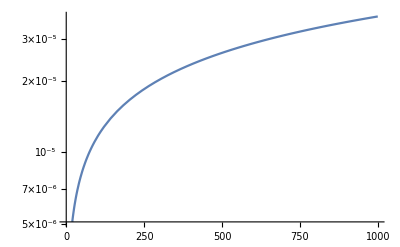

```mathematica
LogPlot[
UniverseModelData[<|"Time"->Quantity[$, "Years"]|>,"ScaleFactor"],{$,.01,1000}]
```

```mathematica
UniverseModelData[Quantity[5,"Years"]]
```

<|AngularDiameterDistance→119568. ly,ComovingDistance→4.63383×10^10 ly,ComovingVolume→4.16782×10^32 ly^3,ConformalTime→1.46245×10^18 s,DarkEnergyDensityRatio→3.61895×10^-17 %,Epoch→radiation dominated, pre-recombination,EventHorizon→6.28729×10^10 ly,HubbleDistance→6.62943×10^11 ly,HubbleParameter→9.37544×10^10 km/(Mpc s),LuminosityDistance→1.79583×10^16 ly,MatterEnergyDensityRatio→0.937573 %,MaximumUniverseAge→∞ yr,ParticleHorizon→4.63424×10^10 ly,RadiationEnergyDensityRatio→99.0624 %,RadiationTemperature→Missing[NotAvailable],Redshift→387548.,ScaleFactor→2.58032×10^-6,TimeAgo→1.38064×10^10 yr,TotalObservableRadiusFraction→0.999913,TransverseComovingDistance→4.63383×10^10 ly,UniverseCurvature→-0.0000839708|>

```mathematica
FormulaData[]//Column;

FormulaData["AbbeNumberHelium"]

$=FormulaData[{"BlackHoleEntropy","AngularMomentum"},{"J"->Quantity[0,""]}]
$//Simplify
```

V AbbeNumber==(-1+n_d RefractiveIndex)/(-n_C RefractiveIndex+n_F RefractiveIndex)

S Entropy==(π k c^3/(G ℏ)) ((Quantity[0,]^2 (1 /c^2))/(M Mass)^2+((1 G/c^2) M Mass+√(((-1 /c^2) Quantity[0,]^2)/(M Mass)^2+(1 G^2/c^4) (M Mass)^2))^2)

(-2 π k G/(ℏ c)) (M Mass)^2+(-2 π k c/ℏ) M Mass √(((-1 /c^2) Quantity[0,]^2)/(M Mass)^2+(1 G^2/c^4) (M Mass)^2)+S Entropy==0

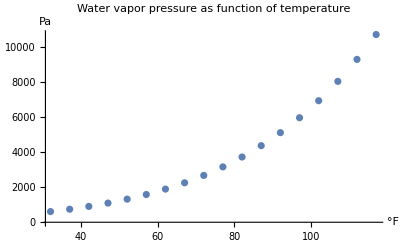
Water vapor pressure as function of temperature
{GoffGratchEquation,Water}
{{32 °F,610.663 Pa},{37 °F,745.539 Pa},{42 °F,906.138 Pa},{47 °F,1096.56 Pa},{52 °F,1321.44 Pa},{57 °F,1585.95 Pa},{62 °F,1895.91 Pa},{67 °F,2257.77 Pa},{72 °F,2678.73 Pa},{77 °F,3166.72 Pa},{82 °F,3730.52 Pa},{87 °F,4379.78 Pa},{92 °F,5125.08 Pa},{97 °F,5978. Pa},{102 °F,6951.17 Pa},{107 °F,8058.31 Pa},{112 °F,9314.32 Pa},{117 °F,10735.3 Pa}}-Graphics-

```mathematica
PR["Water vapor pressure as function of temperature",
NL,$=FormulaLookup["vapor pressure"]//Last,
NL,$p=Table[{Quantity[$f,"Fahrenheit"],FormulaData[$,{"T"-> UnitConvert[Quantity[$f,"Fahrenheit"]]}]},{$f,32,120,5}];
$=$p/.a_==b_->b,
ListPlot[$,PlotLabel->"Water vapor pressure as function of temperature",AxesLabel->Automatic]
]
```

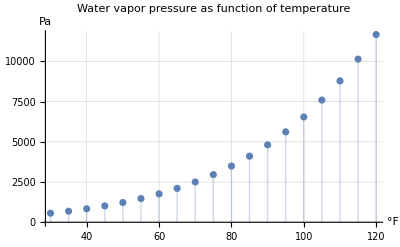

```mathematica
ListPlot[$,PlotLabel->"Water vapor pressure as function of temperature",AxesLabel->Automatic,Joined->False,Filling->Axis,GridLines->Automatic]
```

```mathematica
UnitConvert[ AirTemperatureData[]]
2 UnitConvert[ AirTemperatureData[]]
UnitConvert[AirPressureData[]]
```

{{GoffGratchEquation,Ice},{GoffGratchEquation,Water}}

{GoffGratchEquation,Water}

P_w Pressure==1277.25 Pa

P_w Pressure==6275.7 Pa

283.75 K

567.5 K

101250. kg/(m s^2)

```mathematica
AirTemperatureData[]
UnitConvert[AirTemperatureData[]]
UnitConvert[Quantity[51.6,"Fahrenheit"]]
```

51.08 °F

283.75 K

284.039 K

```mathematica
UnitConvert["g m/s"]
UnitConvert["foot lb s"]
```

1/1000 kg m/s

3389544870828501/2500000000000000 kg m^2/s

```mathematica
PhysicalSystemData[EntityProperty["Action"]]
```

PhysicalSystemData[EntityProperty[Action]]

{{T→ⅇ^(r/(4 G M)) √Abs[-1+r/(2 G M)] (Cosh[t/(4 G M)] HeavisideTheta[2 G M-r]+HeavisideTheta[-2 G M+r] Sinh[t/(4 G M)]),X→ⅇ^(r/(4 G M)) √Abs[-1+r/(2 G M)] (Cosh[t/(4 G M)] HeavisideTheta[-2 G M+r]+HeavisideTheta[2 G M-r] Sinh[t/(4 G M)])}}[$coordSchwarzschildKruskalSzekeres]

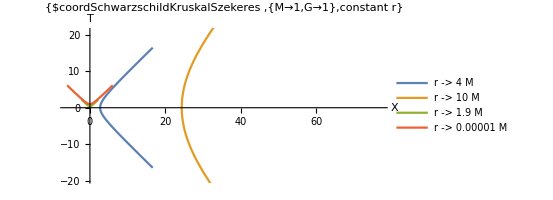

```mathematica
$coordSchwarzschildKruskalSzekeres
$plotSchwarzschildKruskalSzekeres
```

```mathematica
$coordSchwarzschildKruskalSzekeres;
$metricPenroseSchwarzschildKruskalSzekeres;
"What is r for ũ → constant"
$=$metricPenroseSchwarzschildKruskalSzekeres//tuRuleSelect[ũ,{t}];
$=$//Refine[#,r>2 G M&&G>0&&M>0]&//FullSimplify//tuRule1
$=Tan/@$
tuRuleSolve[$,t]//Refine[#,C[1]==0]&//FullSimplify
//
$=$/.Tan[_]->-.0001/.G->1/.  M->1/2;
$=#^2&/@$;$=$
```

What is r for ũ → constant

ũ→-ArcTan[ⅇ^((r-t)/(4 G M)) √(-1+r/(2 G M))]

Tan[ũ]→-ⅇ^((r-t)/(4 G M)) √(-1+r/(2 G M))

{t→r-4 G M Log[-Tan[ũ]/(√(-1+r/(2 G M)))]}

```mathematica
(Entity["Star","Sun"][EntityProperty["Star","Mass"]])^2/Quantity[, "PlanckLength"]//UnitConvert
$=Quantity[, "PlanckMass"]Quantity[, "SpeedOfLight"]/Quantity[, "ReducedPlanckConstant"] //UnitConvert
1/$//UnitSimplify
Entity["Star","Sun"][EntityProperty["Star","Mass"]] Quantity[, "GravitationalConstant"]/Quantity[, "SpeedOfLight"]^2//UnitConvert
Entity["Star","Sun"][EntityProperty["Star","Mass"]] Quantity[, "PlanckLength"]^2//UnitConvert
(*
(Entity["Star","Sun"][EntityProperty["Star","Mass"]])^2 Quantity[, "SpeedOfLight"]^4/Quantity[, "PlanckConstant"]^2//UnitConvert
Quantity[, "Parsecs"]//UnitConvert[#,Quantity[, "LightYears"]]&//N
Quantity[, "LightYears"]//UnitConvert*)
```

2.446×10^95 kg^2/m

6.187×10^34 per meter

1.616×10^-35 m

1477. m

5.194×10^-40 kg m^2

```mathematica
Quantity[, "ReducedPlanckMass"]
```

1 reduced Planck mass

```mathematica
$=Quantity[, "PlanckMass"] Quantity[, "SpeedOfLight"]^2//UnitConvert[#,"GigaElectronvolts"]&
$=Quantity[, "PlanckMass"]Quantity[, "SpeedOfLight"]^2/Quantity[, "PlanckConstant"]//UnitConvert
$t=Quantity[, "PlanckLength"] /Quantity[, "SpeedOfLight"]//UnitConvert
$=Quantity[, "PlanckLength"] //UnitConvert
Entity["Star","Sun"][EntityProperty["Star","Mass"]]/Quantity[, "PlanckMass"] $t
Quantity[, "PlanckLength"]^2 Entity["Star","Sun"][EntityProperty["Star","Mass"]]/Quantity[, "PlanckMass"]/Quantity[, "SpeedOfLight"]^2//UnitConvert
```

1.221×10^19 GeV

2.952×10^42 per second

5.391×10^-44 s

1.616×10^-35 m

4.925×10^-6 s

2.66×10^-49 s^2

```mathematica
1/(Quantity[1,"kg"]/(Quantity[, "PlanckConstant"]/Quantity[, "SpeedOfLight"]))//UnitConvert
($=Quantity[1,"kg"]^-1)->((Quantity[, "PlanckConstant"]/Quantity[, "SpeedOfLight"])$//UnitConvert)
```

2.210219×10^-42 m

1 /kg→2.210219×10^-42 m

```mathematica
$=($=Entity["Star","Sun"][EntityProperty["Star","Mass"]]/Quantity[, "PlanckConstant"] Quantity[, "PlanckLength"]^2)->UnitConvert[$]
$= Quantity[, "PlanckConstant"]/#/Quantity[, "SpeedOfLight"]^2&/@$
UnitConvert[$[[2]]]
```

1.988435×10^30 kg l_P^2/h→7.839×10^-7 s

5.029081×10^-31 h^2/(kg l_P^2 c^2)→1.276×10^6 h/(s c^2)

9.405×10^-45 kg

```mathematica
Sqrt[ℏ c/G]^2
M %
```

(c ℏ)/G

(c M ℏ)/G